## Fit student correctness to various models

```mathematica
SetDirectory[NotebookDirectory[]]
```

/home/bvds/Andes2/LogProcessing/self-improved-tutor

```mathematica
data=Import["guerra-summer-2012.csv"];
```

```mathematica
Take[data,5]
```

{{Section,student,KC,exptProb,controlProb,avgGain,avgLearnSteps},{asu_7e256268bab914fb5asul1_,md5:3f6382444a54a0b87ee01b3eb66502db,draw-vector-aligned-axes,0,0.268941,1,0},{asu_7e256268bab914fb5asul1_,md5:b5a232d14b85a64078d32c873932fe4c,draw-vector-aligned-axes,0.129563,0.51825,1,0},{asu_7e256268bab914fb5asul1_,md5:b37c86f6dcd95008fb661516eec43d27,draw-vector-aligned-axes,0.291582,0.510268,1,0},{asu_7e256268bab914fb5asul1_,md5:f6c03473c87b66e6360c9776fe58f720,draw-vector-aligned-axes,0.156673,0.814712,0.5,4}}

Need to group into KCs, remove header row.

```mathematica
Length[allKCs=Union[Map[#[[3]]&,Rest[data]]]]
```

289

```mathematica
analyzeKC[subdata_]:=Block[{eProbs=Map[#[[4]]&,subdata],cProbs=Map[#[[5]]&,subdata],gains=Map[#[[6]]&,subdata],steps=Map[#[[7]]&,subdata]},
(* Make sure there is data for each condition and that the errors can be estimated. *)
If[0<Total[eProbs] && 0<Total[cProbs] && 0<StandardDeviation[steps] && 0< StandardDeviation[gains],  {subdata[[1,3]],
(* learning step averaged over students for given kc *)
{eProbs.steps/Total[eProbs],
Sqrt[eProbs.eProbs]StandardDeviation[steps]/Total[eProbs]},{cProbs.steps/Total[cProbs],Sqrt[cProbs.cProbs]StandardDeviation[steps]/Total[cProbs]},
(* gain averaged over students for given kc *)
{eProbs.gains/Total[eProbs],Sqrt[eProbs.eProbs]StandardDeviation[gains]/Total[eProbs]},{cProbs.gains/Total[cProbs],Sqrt[cProbs.cProbs]StandardDeviation[steps]/Total[cProbs]}},subdata[[1,3]]]]
```

```mathematica
diffs=Map[Function[kc,analyzeKC[Select[data,(#[[3]]==kc)&]]],allKCs]
```

{accel-at-rest,{accel-constant-speed,{0.688845,0.414002},{0.717565,0.318066},{1.,0.654594},{0.141218,0.318066}},apply-net-work,{area-of-circle,{0.333333,0.308607},{0.834055,0.329629},{0.666667,0.259731},{0.834055,0.329629}},{bernoulli,{0.943006,0.287417},{1.06876,0.286341},{0.283351,0.259523},{0.587135,0.286341}},combo-magnification,{compo-general-case,{17.9033,3.68331},{12.9648,3.1534},{-0.102674,0.193412},{0.0643937,3.1534}},{compo-general-case-unknown,{0.,0.57735},{1.22725,0.418657},{1.,0.558593},{-0.0738432,0.418657}},{compo-parallel-axis,{43.0432,7.42491},{39.4163,7.04056},{-0.104978,0.116877},{-0.0979849,7.04056}},{compo-perpendicular,{13.4579,2.39792},{12.7155,2.331},{-0.256575,0.154187},{-0.258914,2.331}},{compo-z-axis,{2.31073,0.770732},{2.59247,0.730206},{0.720872,0.166064},{0.49074,0.730206}},compo-zero-vector,{continuity,{0.245878,0.190425},{0.491756,0.190425},{0.877061,0.166735},{0.777871,0.190425}},define-amplitude,{define-angle-between-lines,{1.24013,0.368823},{1.25916,0.41346},{0.437042,0.237331},{0.627933,0.41346}},{define-angle-between-vectors,{0.822665,0.62138},{1.38316,0.951557},{0.0914072,0.0690422},{0.153684,0.951557}},define-angular-frequency,define-area,{define-area-at,{0.688845,0.2279},{0.550286,0.218525},{1.,0.0849335},{0.816571,0.218525}},{define-capacitance-var,{1.,0.408248},{0.,0.295806},{1.,0.547723},{0.611819,0.295806}},{define-charge,{6.98787,2.24788},{8.58138,2.04388},{0.0317754,0.21573},{0.0376159,2.04388}},define-coef-friction,{define-compression,{0.262686,0.117815},{0.,0.101884},{0.75,0.139592},{0.787696,0.101884}},{define-current-thru,{5.92374,1.80803},{5.52828,1.61631},{0.236426,0.227432},{0.296492,1.61631}},{define-distance,{3.27829,0.985498},{3.05474,1.01377},{-0.262972,0.228756},{-0.419944,1.01377}},{define-distance-between,{1.49051,0.51554},{0.348293,0.443478},{0.295468,0.241677},{0.481957,0.443478}},{define-duration,{1.24504,1.52151},{3.,2.12132},{0.0158166,0.5917},{-0.666667,2.12132}},{define-electric-power-var,{1.69775,0.425934},{1.82159,0.48259},{0.724562,0.30745},{-0.13812,0.48259}},{define-energy-var,{0.,0.204124},{0.328296,0.188126},{0.,0.240906},{0.188747,0.188126}},{define-flux,{0.,0.308607},{0.898532,0.246191},{0.,0.308607},{0.898532,0.246191}},define-focal-length,{define-frequency,{9.59417,2.11097},{5.32773,2.14933},{-0.311889,0.218526},{0.185232,2.14933}},{define-grav-accel,{0.865904,0.223518},{0.619024,0.195857},{0.658507,0.286838},{0.496999,0.195857}},define-height,{define-image-distance,{0.720971,0.46883},{0.68231,0.46913},{0.519352,0.312553},{0.545127,0.46913}},{define-index-of-refraction,{0.650004,0.810797},{2.08038,0.781067},{1.,0.179449},{0.567389,0.781067}},define-intensity-at,{define-magnification,{0.74264,0.402193},{0.438195,0.404359},{0.504907,0.278406},{0.671354,0.404359}},{define-mass,{14.1005,2.7688},{12.8799,2.6355},{0.0358778,0.146555},{0.0840218,2.6355}},{define-mass-density,{1.8026,0.428918},{0.717391,0.455097},{0.244529,0.236125},{0.764756,0.455097}},{define-moment-of-inertia,{1.0994,0.340568},{0.998723,0.361702},{0.143392,0.287152},{0.11432,0.361702}},define-net-work,{define-object-distance,{0.426208,0.753968},{2.39823,0.772422},{0.680344,0.352249},{-0.15473,0.772422}},{define-period-var,{2.53458,0.415231},{2.36016,0.377886},{-0.431448,0.297881},{-0.58596,0.377886}},{define-pressure,{3.00178,0.946895},{3.73822,1.08372},{0.774106,0.0668315},{0.743513,1.08372}},{define-radius-of-circle,{0.50747,0.350301},{1.17534,0.347834},{0.678205,0.214174},{1.,0.347834}},define-rate-of-change-var,{define-resistance-var,{5.59082,2.14641},{5.22426,1.691},{0.073861,0.391741},{-0.218091,1.691}},{define-revolution-radius,{1.8529,0.562018},{1.7422,0.554569},{0.718048,0.31278},{0.288733,0.554569}},{define-shape-length,{0.960579,0.478503},{1.43838,0.447029},{0.869004,0.213161},{0.44055,0.447029}},{define-slit-separation,{0.,0.127255},{0.298052,0.139059},{0.737314,0.147358},{0.716342,0.139059}},{define-speed,{1.16792,0.398685},{0.577107,0.377795},{0.134495,0.365224},{0.218452,0.377795}},define-spring-constant,{define-stored-energy-var,{0.638261,0.275654},{0.512372,0.308047},{0.24826,0.27256},{0.756186,0.308047}},define-string-tension,define-total-energy,{define-turns,{0.596104,0.248048},{0.624113,0.209267},{0.730736,0.187507},{1.,0.209267}},define-turns-per-length,{define-voltage-across,{4.72825,1.62212},{5.25778,1.37844},{0.426797,0.312823},{0.253396,1.37844}},define-volume,{define-wavelength,{5.28216,1.56325},{3.72453,1.49773},{0.30637,0.220585},{0.442925,1.49773}},define-wavenumber,{define-wave-speed,{1.61663,0.899714},{2.63778,0.77307},{0.598442,0.205822},{0.646237,0.77307}},{define-wnc,{0.525372,0.207806},{0.,0.333333},{0.525372,0.274902},{0.,0.333333}},{define-work,{1.01747,0.376281},{1.50763,0.346302},{0.626735,0.350188},{-0.135139,0.346302}},{definition-syntax,{401.41,101.426},{397.03,91.2399},{0.0187112,0.0651741},{-0.0952586,91.2399}},draw-accelerating,{draw-accel-free-fall,{2.45532,0.38746},{1.76104,0.377155},{-0.333521,0.263727},{0.375829,0.377155}},draw-accel-given-dir,draw-accel-given-zero-net-force,{draw-accel-slow-down,{1.,0.438529},{0.703143,0.237099},{1.,0.448168},{0.726722,0.237099}},{draw-accel-speed-up,{5.98442,1.02558},{5.17226,1.05302},{-0.292045,0.209057},{-0.352378,1.05302}},draw-accel-unknown,draw-ang-accel,draw-ang-accel-slow-down,{draw-ang-accel-speed-up,{0.469646,0.206645},{0.76435,0.238977},{0.681787,0.17896},{0.878669,0.238977}},draw-ang-displacement-rotating,draw-ang-displacement-unknown,{draw-ang-momentum-rotating,{0.973637,0.264479},{0.806971,0.271625},{0.0847346,0.36718},{0.347072,0.271625}},draw-ang-velocity-at-rest,{draw-ang-velocity-rotating,{4.82188,0.933059},{3.20134,0.967692},{0.441695,0.198126},{0.32402,0.967692}},{draw-applied-force,{3.82581,1.0638},{5.41575,0.882514},{0.237789,0.263455},{-0.124406,0.882514}},draw-avg-vel-from-displacement,draw-avg-vel-unknown,{draw-bfield-straight-current,{2.3597,0.582655},{1.43574,0.497773},{0.347975,0.224381},{0.431267,0.497773}},{draw-bforce-charge,{2.80403,0.694732},{2.81945,0.673198},{0.235431,0.21308},{0.199931,0.673198}},draw-bforce-rhr-zero,draw-bforce-unknown-velocity,{draw-body,{46.7589,7.21617},{37.0085,6.82295},{-0.486806,0.173754},{-0.311767,6.82295}},draw-buoyant-force,{draw-centripetal-acceleration,{1.79621,0.539162},{1.32158,0.476815},{0.0227963,0.333986},{0.375048,0.476815}},{draw-compo-form-axes,{16.0069,3.03809},{11.4214,2.64822},{-0.609659,0.28986},{-0.269959,2.64822}},draw-coulomb-force,{draw-coulomb-force-unknown,{0.931672,0.553493},{1.07197,0.478239},{-0.128601,0.380179},{0.413223,0.478239}},{draw-displacement-given-dir,{2.90236,0.514637},{1.46945,0.465041},{-0.481625,0.269998},{-0.0549998,0.465041}},draw-displacement-projectile,{draw-displacement-straight,{2.70714,0.970129},{2.74041,0.932555},{0.428464,0.191452},{0.320169,0.932555}},draw-displacement-unknown,draw-displacement-zero,draw-drag,draw-efield-given-force-dir,draw-electric-force-given-dir,{draw-electric-force-given-field-dir,{0.533426,0.247594},{0.468823,0.213668},{0.292556,0.292794},{0.644443,0.213668}},draw-electric-force-given-field-unknown,draw-energy-axes,{draw-field-given-dir,{3.73415,0.449424},{3.28082,0.427648},{-0.393949,0.216979},{-0.235822,0.427648}},draw-field-unknown,{draw-grav-force,{0.269724,0.188091},{0.424647,0.187573},{0.595414,0.253516},{0.58302,0.187573}},draw-impulse-given-momenta,draw-impulse-given-momenta-unknown-dir,{draw-kinetic-friction,{0.962381,0.43001},{1.39697,0.418277},{0.464225,0.329474},{-0.125463,0.418277}},{draw-line-given-dir,{2.6796,0.592677},{1.74143,0.536672},{0.353036,0.208509},{0.65809,0.536672}},{draw-line-unknown-dir,{1.29837,0.37393},{0.933134,0.383885},{0.659344,0.198886},{0.885421,0.383885}},{draw-momentum-at-rest,{1.00528,0.324436},{0.509429,0.302376},{0.939664,0.143161},{0.968951,0.302376}},{draw-momentum-straight,{1.20946,0.815615},{2.8406,0.849528},{0.540868,0.198498},{0.386619,0.849528}},draw-momentum-straight-unknown,{draw-net-field-given-dir,{0.968627,1.14047},{2.86786,0.923228},{-0.0950287,0.36963},{0.585542,0.923228}},draw-net-field-given-zero,draw-net-field-unknown,{draw-net-force-from-accel,{1.15289,0.397354},{0.507866,0.411503},{0.12588,0.217668},{0.450499,0.411503}},{draw-net-force-from-forces,{0.425958,0.495588},{1.47538,0.655053},{0.832342,0.474489},{-0.737689,0.655053}},draw-net-force-unknown,draw-net-force-zero,draw-net-torque-from-motion,draw-net-torque-non-rotating,draw-net-torque-unknown-dir,{draw-normal,{2.68053,0.971449},{4.07701,0.986423},{-0.49005,0.267916},{-0.189686,0.986423}},draw-opposite-relative-position,draw-point-efield-given-relpos-dir,{draw-point-efield-unknown,{0.768558,0.441824},{1.2409,0.486345},{0.884279,0.152919},{0.875512,0.486345}},{draw-pressure,{2.35079,0.887312},{1.06592,0.761988},{0.845021,0.372607},{0.149504,0.761988}},{draw-projection-axes,{0.315605,0.211879},{0.455356,0.200553},{0.894798,0.195625},{0.595239,0.200553}},{draw-reaction-force,{0.16976,0.692532},{1.63499,0.570312},{-0.04244,0.217854},{0.0949053,0.570312}},{draw-relative-position,{4.74495,0.951296},{4.14504,0.897968},{0.128286,0.233286},{0.0296009,0.897968}},{draw-relative-position-unknown,{1.63245,0.79282},{2.10398,0.693629},{0.346852,0.328407},{0.165211,0.693629}},draw-relative-vel-given-dir,draw-rel-vel-vector-unknown,{draw-spring-force,{0.,0.141934},{0.26462,0.118928},{1.,0.192179},{0.880469,0.118928}},{draw-tension,{8.16222,1.59587},{6.31326,1.58445},{-0.255078,0.202201},{-0.00709492,1.58445}},{draw-torque,{2.34709,0.581121},{1.78943,0.618083},{0.311668,0.211365},{0.813933,0.618083}},draw-unit-vector-given-dir,{draw-unrotated-axes,{13.4356,2.10348},{12.1452,2.08519},{-0.348592,0.195615},{-0.369424,2.08519}},{draw-vector-aligned-axes,{1.15353,0.615189},{1.57828,0.55664},{0.815919,0.169611},{0.588677,0.55664}},{draw-velocity-at-rest,{0.808886,0.503939},{1.91274,0.456859},{0.475432,0.274897},{0.614663,0.456859}},{draw-velocity-curved,{6.44871,1.1221},{5.1808,1.07626},{-0.465371,0.243757},{-0.56278,1.07626}},{draw-velocity-curved-unknown,{0.,0.273542},{0.9677,0.303745},{1.,0.239912},{0.82795,0.303745}},{draw-velocity-momentarily-at-rest,{2.23417,0.532318},{2.95553,0.456068},{0.312061,0.241738},{-0.0191996,0.456068}},{draw-velocity-straight,{12.5882,1.87691},{10.7945,1.80538},{-0.0859056,0.144501},{0.152271,1.80538}},draw-velocity-straight-unknown,{draw-weight,{5.78605,1.79065},{4.94328,1.71436},{0.248986,0.198525},{0.291641,1.71436}},{draw-weight-at-cm,{0.,0.204124},{1.,0.288675},{0.5,0.36411},{1.,0.288675}},{draw-xy-vector-given-compos,{0.,0.2892},{0.854,0.308436},{0.8,0.1446},{0.892441,0.308436}},draw-z-axis-vector-given-compos,{equation-syntax,{291.461,85.0066},{226.729,78.6384},{0.130023,0.0798303},{0.237887,78.6384}},equiv-capacitance-parallel,equiv-capacitance-series,{equiv-resistance-parallel,{0.844941,0.54852},{1.82092,0.458832},{0.826577,0.322717},{0.184046,0.458832}},{equiv-resistance-series,{1.33301,0.9576},{2.66528,0.831239},{0.322286,0.426598},{-0.144763,0.831239}},frequency-of-wave,{given-fraction,{1.,0.57735},{0.566481,0.411841},{-0.5,0.763763},{0.71676,0.411841}},kinetic-friction-law,lens-combo,{lens-eqn,{0.883228,0.508617},{1.36946,0.505853},{0.558386,0.38091},{-0.0847826,0.505853}},lens-eqn-image-at-infinity,lens-eqn-obj-at-infinity,{magnification-eqn,{0.835665,0.264023},{0.,0.291323},{0.470092,0.258645},{0.718428,0.291323}},mass-per-length,{mass-per-length-equation,{0.,0.57735},{0.688845,0.436396},{1.,0.57735},{0.688845,0.436396}},{ntl,{1.,0.301511},{0.,0.213201},{1.,0.467099},{0.,0.213201}},{object-label,{200.295,46.2934},{181.691,44.5388},{-0.0261223,0.134667},{-0.0143451,44.5388}},opposite-relative-position,{pendulum-oscillation,{0.344422,0.276001},{0.611819,0.221111},{0.516634,0.251953},{0.713789,0.221111}},period-of-wave,{pressure-at-open-to-atmosphere,{0.903184,0.334888},{1.31364,0.331384},{0.613061,0.259033},{0.426874,0.331384}},{pressure-force,{1.,0.483046},{0.612265,0.235827},{1.,0.417222},{0.762042,0.235827}},pressure-height-fluid,{sdd-constvel-compo,{0.682245,0.393202},{1.38544,0.353351},{0.475077,0.353006},{0.198412,0.353351}},speed-equals-wave-speed,{spring-law-compression,{0.512372,0.184093},{0.,0.156102},{0.871907,0.121766},{0.626526,0.156102}},{spring-mass-oscillation,{0.424607,0.277608},{0.746949,0.206504},{0.808202,0.209852},{0.91565,0.206504}},wavenumber-lambda-wave,wave-speed-string,{write-angle-direction-known,{1.25501,0.551779},{1.88035,0.479098},{0.204243,0.318283},{-0.223081,0.479098}},{write-angle-direction-known-lines,{0.755242,0.292898},{0.498942,0.351808},{0.460542,0.264936},{1.,0.351808}},write-angle-direction-line,write-ang-momentum,write-ang-sdd,write-archimedes,write-average-rate-of-change,write-avg-vel-compo,{write-capacitance-definition,{4.07814,0.751673},{2.85583,0.750756},{0.153738,0.281957},{0.306037,0.750756}},{write-cap-energy,{0.644126,0.187487},{0.,0.243826},{0.911031,0.164361},{0.595899,0.243826}},{write-centripetal-accel,{0.41106,0.388217},{0.422118,0.259271},{0.79447,0.280415},{0.587606,0.259271}},{write-centripetal-accel-compo,{1.23958,0.437691},{0.308997,0.405842},{0.0778184,0.331711},{0.448573,0.405842}},{write-change-me,{0.815758,0.292502},{1.,0.483046},{1.,0.252644},{0.666667,0.483046}},{write-charge-force-bfield,{0.629822,0.368341},{1.4803,0.302831},{0.453615,0.356187},{0.0868075,0.302831}},{write-charge-force-bfield-mag,{0.407879,0.585005},{1.82019,0.644791},{0.611819,0.404951},{-0.213462,0.644791}},{write-charge-force-efield-compo,{2.61083,0.778324},{2.24499,0.77234},{0.216416,0.362911},{0.100062,0.77234}},{write-charge-force-efield-mag,{0.,0.18422},{0.222045,0.127053},{0.276598,0.215123},{0.349704,0.127053}},write-charge-same-caps-in-branch,write-complimentary-angles,{write-connected-accels,{0.877633,0.289577},{0.407058,0.355588},{0.412294,0.277035},{0.401176,0.355588}},write-cons-angmom,write-cons-linmom-compo,{write-cons-linmom-compo-join-split,{0.,0.225354},{0.579424,0.218652},{0.655578,0.188965},{0.855144,0.218652}},{write-coulomb,{0.,1.08012},{2.52317,0.764582},{0.,0.483046},{1.,0.764582}},{write-coulomb-compo,{2.75676,1.3308},{2.59316,0.980457},{0.151447,0.394769},{0.53966,0.980457}},write-density,{write-electric-power,{1.63942,0.394349},{1.56933,0.445965},{0.463725,0.208659},{0.890595,0.445965}},{write-energy-cons,{1.26708,0.347049},{0.652548,0.332875},{0.425135,0.338921},{0.365717,0.332875}},{write-equality,{1.11487,0.535686},{1.65311,0.434658},{0.21391,0.32415},{0.331233,0.434658}},write-faradays-law,write-flux-constant-field,write-flux-zero,{write-free-fall-accel,{1.29258,0.314806},{0.827861,0.302847},{0.454418,0.289815},{0.738976,0.302847}},{write-g-on-earth,{1.75537,0.480505},{1.38258,0.512814},{0.340093,0.205307},{0.486047,0.512814}},{write-grav-energy,{2.95483,1.15341},{3.52026,1.02306},{0.622443,0.285332},{0.427812,1.02306}},{write-harmonic-of,{2.39697,1.12571},{3.15274,1.13591},{0.545278,0.256497},{0.447405,1.13591}},{write-height-dy,{0.724698,0.283705},{0.326045,0.309135},{0.659484,0.216959},{0.55817,0.309135}},write-i-compound,write-i-hoop-cm,write-impulse-compo,write-impulse-momentum-compo,write-inside-solenoid-bfield,write-i-rod-cm,write-junction-rule,write-junction-rule-cap,{write-kinetic-energy,{3.06741,0.836601},{3.6916,0.804638},{0.705596,0.196168},{0.275003,0.804638}},{write-known-value-eqn,{133.992,29.2552},{116.696,27.3922},{0.0387576,0.124224},{0.0138199,27.3922}},write-linear-vel,{write-lk-no-s-compo,{1.7154,0.467194},{2.57897,0.520139},{-0.231148,0.252602},{-0.16485,0.520139}},{write-lk-no-t-compo,{0.442599,0.205913},{0.406906,0.231838},{0.442599,0.261569},{0.42215,0.231838}},{write-lk-no-vf-compo,{1.75009,0.579278},{1.06989,0.493942},{-0.278806,0.361936},{-0.131607,0.493942}},{write-loop-rule-capacitors,{2.71225,1.07755},{3.05759,1.11391},{0.212595,0.285982},{0.452889,1.11391}},{write-loop-rule-resistors,{0.679015,0.774203},{2.14201,0.64814},{0.951453,0.285964},{0.169503,0.64814}},{write-mag-torque,{1.,0.299022},{0.770723,0.310791},{0.282435,0.419088},{0.321327,0.310791}},write-mass-compound,{write-momentum-compo,{3.74694,1.08266},{3.27949,1.06603},{-0.14153,0.309731},{0.179923,1.06603}},{write-net-field-compo,{0.356275,0.335711},{0.980968,0.36619},{1.,0.227747},{0.493972,0.36619}},{write-net-force-compo,{3.54735,0.937834},{1.9668,0.885441},{0.146443,0.249502},{0.385973,0.885441}},write-net-torque,{write-nfl-compo,{4.07418,0.835086},{4.469,0.82539},{-0.0599491,0.236533},{-0.162535,0.82539}},write-nfl-rot,{write-nsl-compo,{5.53525,1.59859},{6.83014,1.59394},{0.029327,0.221213},{0.257152,1.59394}},{write-nsl-net-compo,{0.705108,0.35077},{0.,0.666667},{0.0307622,0.322203},{0.,0.666667}},write-nsl-rot-compo,write-nsl-rot-net,{write-ntl-vector,{1.8209,0.84546},{3.,1.3562},{1.,0.463826},{-1.,1.3562}},write-null-spring-energy,{write-ohms-law,{6.9199,1.54421},{4.45816,1.22181},{-0.379831,0.309628},{0.298487,1.22181}},write-period-circular,{write-point-charge-efield-compo,{1.03728,0.743927},{3.11679,0.839758},{0.842522,0.0851601},{0.940123,0.839758}},write-polarizer-intensity,write-potential-energy,write-pyth-thm,{write-right-triangle-tangent,{0.356275,0.22427},{0.525372,0.205909},{1.,0.144765},{0.881343,0.205909}},{write-rk-no-s,{0.450434,0.190828},{0.298052,0.211245},{0.241483,0.210489},{0.447078,0.211245}},write-rk-no-t,write-rk-no-vf,write-rolling-vel,write-rotational-energy,{write-sdd,{2.07935,0.445565},{1.24468,0.435296},{-0.175734,0.297677},{0.374931,0.435296}},{write-single-loop-rule,{0.,0.288675},{1.,0.288675},{1.,0.450168},{0.5,0.288675}},{write-slit-interference,{1.44926,0.470432},{0.62641,0.469187},{0.283884,0.318602},{0.454071,0.469187}},write-snells-law,{write-speed-of-wave,{2.79954,1.16628},{2.37362,1.03231},{0.757446,0.198743},{0.59196,1.03231}},{write-spring-energy,{1.01963,0.268443},{0.632335,0.243645},{0.22493,0.273093},{0.00363833,0.243645}},{write-straight-wire-bfield,{0.596104,0.251566},{0.774646,0.219513},{0.730736,0.187507},{1.,0.219513}},write-sum-disp-compo,write-sum-distances,{write-sum-times,{0.,0.363137},{0.712333,0.197456},{1.,0.468807},{1.,0.197456}},{write-tensions-equal,{1.52466,0.379128},{1.14545,0.340995},{0.6167,0.33951},{0.0479769,0.340995}},{write-torque,{2.51156,1.17467},{2.63323,1.0828},{-0.00778242,0.442564},{0.321207,1.0828}},{write-total-energy-top,{1.53072,0.519991},{1.64075,0.487111},{0.611821,0.297313},{0.316717,0.487111}},write-total-internal-reflection,write-transformer-power,write-turns-per-length,write-ug,write-ug-circular,write-unit-vector-mag,write-value-of-atmosphere,{write-vector-magnitude,{1.56326,0.701552},{1.70008,0.635315},{0.584769,0.220008},{0.873826,0.635315}},{write-wave-speed-light,{0.288009,0.287384},{1.30517,0.37418},{0.362154,0.215792},{0.390411,0.37418}},write-wave-speed-refraction,write-wnc,{write-work,{1.34463,0.582637},{2.36081,0.573134},{0.0774319,0.277454},{0.928525,0.573134}},write-work-energy,{wt-law,{10.5933,1.85242},{7.70849,1.92343},{-0.0684512,0.180445},{0.052017,1.92343}},wt-law-cm}

Scatter plot showing number of steps before mastery for each KC in each experimetal condition.

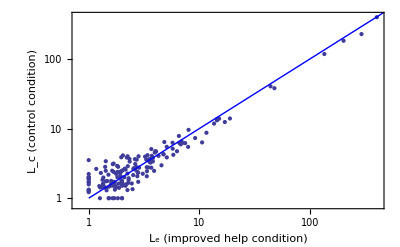

```mathematica
scatterStep=Block[{data=Map[(1+{#[[2,1]],#[[3,1]]})&,Select[diffs,#[[0]]==List&]]},ListLogLogPlot[data,
(* Seems to be a bug in PlotRange->All, so do this by hand. *) 
PlotRange->{#,#}&[{0.8,Max[Flatten[data]]+10}],Epilog->{Blue,Line[{{0,0},{10,10}}]},Axes->False,Frame->True,FrameLabel->{"L_e (improved help condition)","L_c (control condition)"},BaseStyle->{FontSize->12}]]
```

```mathematica
Export["scatter-step.eps",scatterStep]
```

scatter-step.eps

```mathematica
xx=Apply[Function[{val,err},Block[{weights=1/err^2},{Length[val],(* regular mean *) {Mean[val],Sqrt[err.err]/Length[val]},(* maximum likelihood maximizing weighed mean *){val.weights/Total[weights],1/Sqrt[Total[weights]]}}]],Transpose[Map[{#[[2,1]]-#[[3,1]],Sqrt[(#[[2,2]])^2+(#[[3,2]])^2]}&,Select[diffs,#[[0]]==List&]]]]
```

{164,{0.755752,1.19191},{-0.0467735,0.0399037}}

This is the  one-tailed p-value from a Z-test

```mathematica
Block[{z=xx[[3,1]]/xx[[3,2]]},(1+Erf[-Abs[z]/Sqrt[2]])/2]
```

0.120566

Select only cases where positive learning was seen in both conditions.  We see that there is almost no difference in the change in number of steps.

```mathematica
xx2=Apply[Function[{val,err},Block[{weights=1/err^2},{Length[val],(* regular mean *) {Mean[val],Sqrt[err.err]/Length[val]},(* maximum likelihood maximizing weighed mean *){val.weights/Total[weights],1/Sqrt[Total[weights]]}}]],Transpose[Map[{#[[2,1]]-#[[3,1]],Sqrt[(#[[2,2]])^2+(#[[3,2]])^2]}&,Select[diffs,If[#[[0]]==List , 0<#[[4,1]] && 0<#[[5,1]]]&]]]]
```

{112,{0.688646,1.09809},{-0.0419361,0.0429396}}

```mathematica
<<HypothesisTesting`
```

Scatter plot showing performance gain 1-s-g for each KC in each experimetal condition.

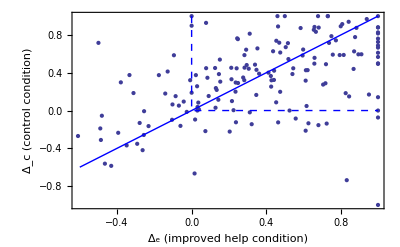

```mathematica
scatterGain=ListPlot[Map[{#[[4,1]],#[[5,1]]}&,Select[diffs,#[[0]]==List&]],PlotRange->All,Epilog->{Blue,Line[{{-.6,-.6},{1,1}}],Dashed,Line[{{0,1},{0,0},{1,0}}]},Frame->True,Axes->False,FrameLabel->{"Δ_e (improved help condition)","Δ_c (control condition)"},BaseStyle->{FontSize->12}]
```

```mathematica
Export["scatter-gain.eps",scatterGain]
```

scatter-gain.eps

```mathematica
yy=Apply[Function[{val,err},Block[{weights=1/err^2},{Length[val],{Mean[val],Sqrt[err.err]/Length[val]},{val.weights/Total[weights],1/Sqrt[Total[weights]]}}]],Transpose[Map[{#[[4,1]]-#[[5,1]],Sqrt[(#[[4,2]])^2+(#[[5,2]])^2]}&,Select[diffs,#[[0]]==List&]]]]
```

{164,{0.0278803,0.805984},{0.00799313,0.0378017}}

This is the  one-tailed p-value from a Z-test

```mathematica
Block[{z=yy[[3,1]]/yy[[3,2]]},(1+Erf[-Abs[z]/Sqrt[2]])/2]
```

0.416268